```mathematica
Quit
```

```mathematica
1;
```

학습 목표
Mathematica로 구현된 Sin[x] 함수를 학습하는 아래 머신 러닝 예제를 이해하고.
머신 러닝의 세부 설정들을 변경해 보며 어떤 일이 벌어지는 지 탐구해 보자.

학습 대상
Data 수 바꿔보기
Data 범위 바꿔보기

Activation Function 바꿔보기
Layer 개수 바꿔보기
Node 개수 바꿔보기

Learning Rate 바꿔보기
Optimizer 바꿔보기

## Example

```mathematica
(* 데이터 수 *)dataN=10;
(* 데이터 범위 *)dataRange={0,2π};

BigDATA={Table[{x}//N,{x,dataRange[[1]],dataRange[[2]],dataRange[[2]]/dataN}],Table[{Sin[x]}//N,{x,dataRange[[1]],dataRange[[2]],dataRange[[2]]/dataN}]}
```

{{{0.},{0.628319},{1.25664},{1.88496},{2.51327},{3.14159},{3.76991},{4.39823},{5.02655},{5.65487},{6.28319}},{{0.},{0.587785},{0.951057},{0.951057},{0.587785},{0.},{-0.587785},{-0.951057},{-0.951057},{-0.587785},{0.}}}

```mathematica
NN=NetInitialize@NetChain[{LinearLayer[(*Node*)3,"Input"->1],(*Activation Function; Ex. Tanh, Ramp, LogisticSigmoid, Sin, Cos, ...*)Tanh,LinearLayer[5],Tanh,LinearLayer[1]}]
NetGraph[NN]
```

NetChain[…]

NetGraph[…]

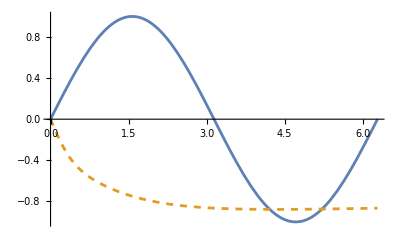

```mathematica
(* 학습 전 *)
Plot[{Sin[x],NN[x]},{x,0,2π},PlotStyle->{Null,Dashed}]
```

```mathematica
train=NetTrain[NN,<|"Input"->BigDATA[[1]],"Output"->BigDATA[[2]]|>,Method->(*Optimizer*)"RMSProp",LearningRate->10^-4,MaxTrainingRounds->10^4]
```

NetChain[…]

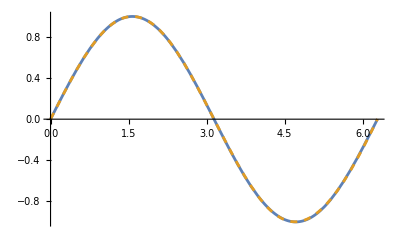

```mathematica
(* 학습 후 *)
Plot[{Sin[x],train[x]},{x,0,2π},PlotStyle->{Null,Dashed}]
```

## 자유롭게 변경해 보세요!

```mathematica
(* 데이터 수 *)dataN=10;
(* 데이터 범위 *)dataRange={0,2π};
F[x_]=Abs[x-2]
BigDATA2={Table[{x}//N,{x,dataRange[[1]],dataRange[[2]],dataRange[[2]]/dataN}],Table[{F[x]}//N,{x,dataRange[[1]],dataRange[[2]],dataRange[[2]]/dataN}]}
```

Abs[-2+x]

{{{0.},{0.628319},{1.25664},{1.88496},{2.51327},{3.14159},{3.76991},{4.39823},{5.02655},{5.65487},{6.28319}},{{2.},{1.37168},{0.743363},{0.115044},{0.513274},{1.14159},{1.76991},{2.39823},{3.02655},{3.65487},{4.28319}}}

```mathematica
NN2=NetInitialize@NetChain[{LinearLayer[(*Node*)3,"Input"->1],Sin,LinearLayer[10],Sin,LinearLayer[10],Sin,LinearLayer[1]}]
NetGraph[NN2]
```

NetChain[…]

NetGraph[…]

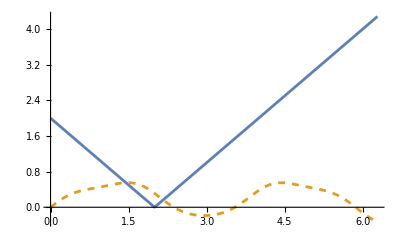

```mathematica
(* 학습 전 *)
Plot[{F[x],NN2[x]},{x,0,2π},PlotStyle->{Null,Dashed}]
```

```mathematica
train2=NetTrain[NN2,<|"Input"->BigDATA2[[1]],"Output"->BigDATA2[[2]]|>,Method->(*Optimizer*)"RMSProp",LearningRate->10^-5,MaxTrainingRounds->10^4]
```

NetChain[…]

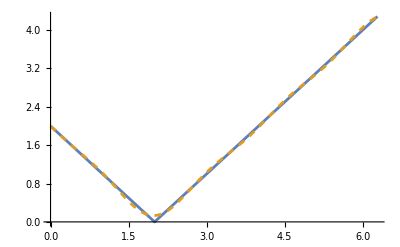

```mathematica
(* 학습 후 *)
Plot[{F[x],train2[x]},{x,0,2π},PlotStyle->{Null,Dashed}]
```